## in 2D:

```mathematica
Clear[vec,CC,cos,u,dx,dy,dz,curlu,curlu2,x,y,z];
CC=10;
cos=Cos[CC*(x^2+y^2)]*Cos[CC*(x^2+y^2)];
u[x_,y_]=cos*{y,-x};
u1=Dot[u[x,y],{1,0}];
u2=Dot[u[x,y],{0,1}];
curlu[x_,y_]=D[u2,x]-D[u1,y];
u[x,y]//MatrixForm//TraditionalForm
curlu[x,y]//TraditionalForm
```

(y cos^2(10 (x^2+y^2))
-x cos^2(10 (x^2+y^2)))

-2 cos^2(10 (x^2+y^2))+40 x^2 sin(10 (x^2+y^2)) cos(10 (x^2+y^2))+40 y^2 sin(10 (x^2+y^2)) cos(10 (x^2+y^2))

```mathematica
R=1/2*Sqrt[2*Pi/CC];
x=0.13;
y=Sqrt[R^2-x^2];
u[x,y]
curlu[x,y]
```

{1.4038×10^-33,-4.87422×10^-34}

3.84734×10^-16

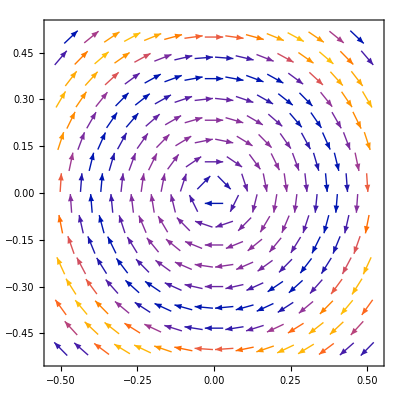

```mathematica
Clear[x,y];
p1=VectorPlot3D[u[x,y,z],{x,-0.5,0.5},{y,-0.5,0.5},{z,-0.5,0.5}];
p2=VectorPlot[u[x,y],{x,-0.5,0.5},{y,-0.5,0.5}];
Show[p2]
```